## Computation of massive Spin-0 quasi-bound states in Kerr spacetime

#### Inputs

```mathematica
Quit[]
```

code based on the method in paper 2204.09335, hereafter used for references

```mathematica
M=1; (*BH mass*)
a=95/100 M; (*BH spin, a<M*)
l0=5; (*field spheroidal l parameter*)
m=4; (*field spheroidal m parameter*)
n0=4;(*field overtone number*)
μ=30190199402717055 / 10;(*field mass (m x G)? *)
L=8;(*field spherical harmonic truncation l-eigenstate*)
Npoints=60;(*number of Chebyshev interpolation points- run from home*)
Iter=40; (*number of iterations for the non-linear inversion*)
digits=30;
```

#### Chebyshev interpolation of the field equation

```mathematica
ClearAll[rplus,rminus,Pplus,Pminus,Aplus,Aminus,Δ,ω,c,l,j,r,θ,ϕ,ν,ζ,w,ζmap,Dζmap,DDζmap,F,DF,DDF,rmap,k,kk,nn,C1,C2,C3plus,C3minus,B,MatrixOp,MatrixEq,ReorgMatrixEq,DMatrixOp,ln,jk, n]

(*Fixing numerical precision*)

$MinPrecision=digits;
$MaxPrecision=digits+10;
$MaxExtraPrecision=digits+10;

(*Defining auxiliary quantities*)

rminus=M-√(M^2-a^2);
rplus=M+√(M^2-a^2);
Δ[r_]:=r^2-2 M r +a^2;
Pplus=(m a-2 ω M rplus)/(rplus-rminus);
Pminus=(m a-2 ω M rminus)/(rplus-rminus);
Aplus=2((m a -2 ω M^2)/(rplus-rminus))^2-4 ω^2 M^2+(μ^2-2 ω^2)M(rplus-rminus)+(2 M^2-a^2)(μ^2-ω^2);
Aminus=2((m a -2 ω M^2)/(rplus-rminus))^2-4 ω^2 M^2-(μ^2-2 ω^2)M(rplus-rminus)+(2 M^2-a^2)(μ^2-ω^2);
ω=μ √(1-(μ^2 M^2)/ν^2); (*Hydrogenic parametrization of ω*)

(*Defining couplings among l-states, see eq. 31-32*)

c[l_,j_]:=If[j-2≤l≤j+2&&-l≤m≤l&&-j≤m≤j,
(1/3)KroneckerDelta[l,j]+ (2 /3)√((2 j+1)/(2 l+1))ClebschGordan[{j,m},{2,0},{l,m}]ClebschGordan[{j,0},{2,0},{l,0}],
(1/3)KroneckerDelta[l,j]];

(*Defining ζ-r map, see eq. 27-28*)

ζmap[r_]:=(r-√(4 rplus(r-rminus)+rminus^2))/(r-rminus);
rmap[ζ_]:=(-rminus+4 rplus+rminus ζ^2)/(-1+ζ)^2;

(*Defining derivatives of the ζ-r map*)

Dζmap[r_]:=(rminus^2+2 r rplus-rminus (2 rplus+√(rminus^2+4 r rplus-4 rminus rplus)))/((r-rminus)^2 √(rminus^2+4 r rplus-4 rminus rplus));
DDζmap[r_]:=1/(r-rminus)^3 2 (r+(2 (r-rminus)^2 rplus^2)/((rminus^2+4 r rplus-4 rminus rplus)^(3/2))-√(rminus^2+4 r rplus-4 rminus rplus)-(r-rminus) (1-(2 rplus)/(√(rminus^2+4 r rplus-4 rminus rplus))));
(*Defining Chebyshev interpolation points, as in eq 37-38*)

Do[
ζ[k]=Cos[(Pi(2 k+1))/(2(Npoints+1))]; (*Chebyshev nodes*)
w[k]=Sin[(2 Pi k(Npoints+2)+Pi)/(2(Npoints+1))]; (*Chebyshev weights*)
,{k,0,Npoints}];

(*Defining derivative matrix in the polynomial base, eq 40*)

Do[
If[k≠n,
DerivP[k,n]=N[(w[k]/w[n])/(ζ[n]-ζ[k]),digits],
DerivP[k,n]=-Sum[If[kk≠n,N[(w[kk]/w[n])/(ζ[n]-ζ[kk]),digits],0],{kk,0,Npoints}]
];
,{k,0,Npoints},{n,0,Npoints}];

(*Defining second derivative matrix in the polynomial base*)

Do[
If[k≠n,
DDerivP[k,n]=2 DerivP[k,n]DerivP[n,n]-(2 DerivP[k,n])/(ζ[n]-ζ[k]),
DDerivP[k,n]=2 DerivP[k,n]DerivP[n,n]+Sum[If[kk≠n,(2 DerivP[kk,n])/(ζ[n]-ζ[kk]),0],{kk,0,Npoints}]
];
,{k,0,Npoints},{n,0,Npoints}];

(*Defining asymptotic behaviour of field ansatz. The boundary conditions here are different than the one of eq 26 in the paper (there we were looking for QNM boundaries), but can rather be found in eq 4.9 here 1908.10370)*)

F[r_]:=((r-rplus)/(r-rminus))^(I Pplus)(r-rminus)^(-1+ν-(2 μ^2 M^2)/ν)E^(-(μ^2 M)/ν(r-rplus));(*It describes asymptotic behaviour*)
DF[r_]:=-(1/ν)ⅇ^(-(M (r-rplus) μ^2)/ν) (r-rminus)^(-3-(2 M^2 μ^2)/ν+ν) ((r-rplus)/(r-rminus))^(-1+ⅈ Pplus) (2 M^2 (r-rplus) μ^2+M (r-rminus) (r-rplus) μ^2+ν (r+ⅈ Pplus (rminus-rplus)+rplus (-1+ν)-r ν)); (*First derivative of F[r]*)
DDF[r_]:=(1/((r-rplus)^2 ν^2))ⅇ^(-(M (r-rplus) μ^2)/ν) (r-rminus)^(-3-(2 M^2 μ^2)/ν+ν) ((r-rplus)/(r-rminus))^(ⅈ Pplus) (4 M^4 (r-rplus)^2 μ^4+4 M^3 (r-rminus) (r-rplus)^2 μ^4-2 M (r-rminus) (r-rplus) μ^2 ν (-ⅈ Pplus (rminus-rplus)+rplus+r (-1+ν)-rplus ν)+M^2 (r-rplus) μ^2 (r^3 μ^2-rminus^2 rplus μ^2-r^2 (2 rminus+rplus) μ^2+4 ⅈ Pplus rminus ν+2 rplus ν (-3-2 ⅈ Pplus+2 ν)+r (rminus^2 μ^2+2 rminus rplus μ^2+2 (3-2 ν) ν))+ν^2 (-Pplus^2 (rminus-rplus)^2-ⅈ Pplus (rminus-rplus) (rminus+3 rplus-2 rplus ν)+2 r (-2+ν) (-ⅈ Pplus (rminus-rplus)+rplus-rplus ν)+r^2 (2-3 ν+ν^2)+rplus^2 (2-3 ν+ν^2))); (*Second derivative of F[r]*)


(*Building the equation coefficients, eq 33-34*)

Do[C1[l,n]=N[(1/(rmap[ζ[n]]-rplus)+1/(rmap[ζ[n]]-rminus))1/Dζmap[rmap[ζ[n]]]+(2 DF[rmap[ζ[n]]])/F[rmap[ζ[n]]] 1/Dζmap[rmap[ζ[n]]]+DDζmap[rmap[ζ[n]]]/(Dζmap[rmap[ζ[n]]])^2,digits];
C2[l,n]=N[1/(Dζmap[rmap[ζ[n]]])^2 DDF[rmap[ζ[n]]]/F[rmap[ζ[n]]]+(1/(rmap[ζ[n]]-rplus)+1/(rmap[ζ[n]]-rminus))1/(Dζmap[rmap[ζ[n]]])^2 DF[rmap[ζ[n]]]/F[rmap[ζ[n]]]+1/(Dζmap[rmap[ζ[n]]])^2(Pplus^2/(rmap[ζ[n]]-rplus)^2+Pminus^2/(rmap[ζ[n]]-rminus)^2-Aplus/((rplus-rminus)(rmap[ζ[n]]-rplus))+Aminus/((rplus-rminus)(rmap[ζ[n]]-rminus))-(μ^2-ω^2))-1/(Dζmap[rmap[ζ[n]]])^2 1/Δ[rmap[ζ[n]]](l(l+1)+a^2 c[l,l](μ^2-ω^2)),digits];
C3plus[l,n]=N[-1/(Dζmap[rmap[ζ[n]]])^2 1/Δ[rmap[ζ[n]]] a^2(μ^2-ω^2)c[l,l+2],digits];
C3minus[l,n]=N[-1/(Dζmap[rmap[ζ[n]]])^2 1/Δ[rmap[ζ[n]]] a^2(μ^2-ω^2)c[l,l-2],digits];
,{l,0,L},{n,0,Npoints}];

(*Building the matrix equation eq 39*)

Do[
MatrixEq[l,n]=Sum[(DDerivP[k,n]+C1[l,n]DerivP[k,n]+C2[l,n]KroneckerDelta[k,n])B[l,k]+C3minus[l,n]B[l-2,k]KroneckerDelta[k,n]+C3plus[l,n]B[l+2,k]KroneckerDelta[k,n],{k,0,Npoints}];
,{l,0,L},{n,0,Npoints}]; (*Field equation in interpolated form, B is the super-vector describing a solution*)

(*Truncation at l=L*)

Do[
B[L+1,k]=0;
B[L+2,k]=0;
B[-1,k]=0;
B[-2,k]=0;
,{k,0,Npoints}];

(*Extracting the matrix operator*)

counter=1;
Do[
ReorgB[counter]=B[j,k];
ReorgMatrixEq[counter]=MatrixEq[j,k]; 
counter++;
,{j,0,L},{k,0,Npoints}]; (*It re-organizes the multi-dimensional matrix as a 2D matrix*)

ReorgBVector=Table[ReorgB[jk],{jk,1,(L+1)(Npoints+1)}];
ReorgMatrixEqVector=Table[ReorgMatrixEq[ln],{ln,1,(L+1)(Npoints+1)}];

MatrixOp=Normal@CoefficientArrays[ReorgMatrixEqVector,ReorgBVector][[2]]; (*2D Matrix of the field equation*)
DMatrixOp=D[MatrixOp,ν]; (*ν-derivative of the 2D matrix of the field equation*)
```

$MaxPrecision::prec: In increasing internal precision while attempting to evaluate 1/(Cos[π/122]-Cos[(3 π)/122]), the limit $MaxPrecision = 40. was reached. Increasing the value of $MaxPrecision may help resolve the uncertainty.

$MaxPrecision::prec: In increasing internal precision while attempting to evaluate 1/(Cos[π/122]-Cos[(5 π)/122]), the limit $MaxPrecision = 40. was reached. Increasing the value of $MaxPrecision may help resolve the uncertainty.

$MaxPrecision::prec: In increasing internal precision while attempting to evaluate 1/(Cos[π/122]-Cos[(7 π)/122]), the limit $MaxPrecision = 40. was reached. Increasing the value of $MaxPrecision may help resolve the uncertainty.

General::stop: Further output of $MaxPrecision::prec will be suppressed during this calculation.

#### Nonlinear inverse iteration

```mathematica
ClearAll[Nν,i,Bnum,BnumNorm,z,x,ReorgB0, R, A, b]

(*Analytic definition of the hydrogenic frequency guess solution*)

Nν[0]=N[l0+1+n0+I (μ M)^(4 l0+2)((a m)/M-2 μ rplus)(2^(4 l0+2) Factorial[2 l0+1+n0])/((l0+1+n0)^(2 l0+1)Factorial[n0])(Factorial[l0]/(Factorial[2 l0] Factorial[2 l0 +1]))^2 Product[j^2(1-a^2/M^2)+((a m)/M-2 μ rplus)^2,{j,1,l0}],digits]; (*Hydrogenic frequency parameter ν*)
R[r_]:=((2 r M μ^2)/(l0+n0+1))^l0 E^(-(r M μ^2)/(l0+n0+1))LaguerreL[n0,2 l0+1,(2 r M μ^2)/(l0+n0+1)]; (*Hydrogenic radial wave function*)

(*Construction of the vector of the hydrogenic guess solution*)

counter=1;
Do[
ReorgB0[counter]=((KroneckerDelta[j,l0]R[rmap[ζ[k]]])/F[rmap[ζ[k]]])/.{ν->Nν[0]};
counter++;
,{j,0,L},{k,0,Npoints}];

Bnum[0]=Table[ReorgB0[jk],{jk,1,(L+1)(Npoints+1)}];
BnumNorm[0]=Bnum[0]/(√(Conjugate[Bnum[0]].Bnum[0]));
```

$MaxPrecision::prec: In increasing internal precision while attempting to evaluate -1-(√39)/20+(-1+(√39)/20+4 (1+(√39)/20)+(1-(√39)/20) Cos[π/122]^2)/(-1+Cos[π/122])^2, the limit $MaxPrecision = 40. was reached. Increasing the value of $MaxPrecision may help resolve the uncertainty.

$MaxPrecision::prec: In increasing internal precision while attempting to evaluate -(36457925599032688978756655514921 (-1+(√39)/20+4 (1+(√39)/20)+(1-(√39)/20) Cos[π/122]^2))/(40 (-1+Cos[π/122])^2), the limit $MaxPrecision = 40. was reached. Increasing the value of $MaxPrecision may help resolve the uncertainty.

General::unfl: Underflow occurred in computation.

$MaxPrecision::prec: In increasing internal precision while attempting to evaluate 1+(√39)/20, the limit $MaxPrecision = 40. was reached. Increasing the value of $MaxPrecision may help resolve the uncertainty.

General::stop: Further output of $MaxPrecision::prec will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
(*Computation of the solution through non-linear inverse iteration*)

VEC=Table[E^(I jk Pi/((L+1)(Npoints+1)))/(√((L+1)(Npoints+1))),{jk,1,(L+1)(Npoints+1)}]; (*Normalization vector*)
Do[
A[i]=MatrixOp/.{ν->Nν[i]};
b[i]=(DMatrixOp.BnumNorm[i])/.{ν->Nν[i]};
Bnum[i+1]=LinearSolve[A[i],b[i]];
Nν[i+1]=Nν[i]-(Conjugate[VEC].BnumNorm[i])/(Conjugate[VEC].Bnum[i+1]);
BnumNorm[i+1]=Bnum[i+1]/(√(Conjugate[Bnum[i+1]].Bnum[i+1]));
,{i,0,Iter-1}]; (*Non-linear inverse iteration*)
```

LinearSolve::mindet: Input matrix contains an indeterminate entry.

#### Result

```mathematica
Print[Nν[0]];(*Prints guess for ν*)
Print[Nν[Iter]]; (*Prints result for ν*)

Print[M μ √(1-(μ^2 M^2)/(Nν[0])^2)];(*Prints guess for frequency*)
Print[M μ √(1-(μ^2 M^2)/(Nν[Iter])^2)];(*Prints result for frequency*)
```

3.+5.35299964768121445193534116823×10^-14 ⅈ

2.99654076476035618104015803627+2.07406339725738427450833536617×10^-14 ⅈ

0.0819693627210123483029554535483108+1.09354661738694152364528015246×10^-18 ⅈ

0.0819692919309915642591929199031444+4.25173005012231682831505058554×10^-19 ⅈ

```mathematica
(*now we plot the wavefunction, by reinserting the Bs and omega obtained from this method in the initial ansatz*)
```

```mathematica
Clear[ω]
```

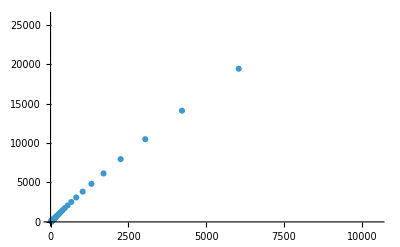

```mathematica
ListPlot[Table[{rmap[ζ[j]],Abs[(((r-rplus)/(r-rminus))^(I Pplus)(r-rminus)^(-1+(μ^2 M)/(√(μ^2-ω^2))-2M √(μ^2-ω^2))E^(-√(μ^2-ω^2)(r-rplus))BnumNorm[Iter][[j+1(Npoints+1)]](*[[j+1(Npoints+1)]]*))/.{ω->μ √(1-(μ^2 M^2)/(Nν[Iter])^2),r->rmap[ζ[j]]}]},{j,1,Npoints}], PlotRange->Automatic]
```

```mathematica
(*Note how the points are focused in the near zone and much less dense far away. This is a consequence of the chosen radial map. lets interpolate this*)
```

```mathematica
prova=Table[{rmap[ζ[j]],Abs[(((r-rplus)/(r-rminus))^(I Pplus)(r-rminus)^(-1+(μ^2 M)/(√(μ^2-ω^2))-2M √(μ^2-ω^2))E^(-√(μ^2-ω^2)(r-rplus))BnumNorm[Iter][[j+1(Npoints+1)]](*[[j+1(Npoints+1)]]*))/.{ω->μ √(1-(μ^2 M^2)/(Nν[Iter])^2),r->rmap[ζ[j]]}]},{j,1,Npoints}]//Quiet;
```

```mathematica
function=Interpolation[prova]
```

InterpolatingFunction[…]

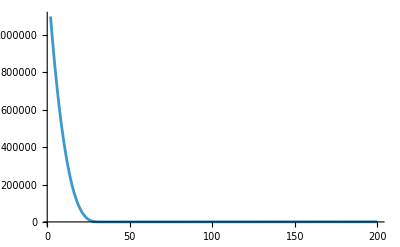

```mathematica
Plot[function[r],{r,2.01,200}, PlotRange->All]
```

```mathematica
(*We now find the same funciton by plugging the eigenvalue obtained from Baumann's method in to the Heun analytic ansatz. We do so below. NB we need the spheroidal eigenvalue to do so. While we can generate it easily for arbitrary spin, for simplicity we here focus on the a=0 case where such eigenvalue is known analytically to be l(l+1)*)
```

```mathematica
ω=μ √(1-(μ^2 M^2)/(Nν[Iter])^2);
a=0;
```

```mathematica
γplussq=μ^2rplus^2-ω^2(4 M^2+2 M rplus+rplus^2);
γminussq=μ^2rminus^2-ω^2(4 M^2+2 M rminus+rminus^2);
λlm=l0(l0+1);
```

$MaxPrecision::prec: In increasing internal precision while attempting to evaluate 4+2 (1+(√39)/20)+(1+(√39)/20)^2, the limit $MaxPrecision = 40. was reached. Increasing the value of $MaxPrecision may help resolve the uncertainty.

$MaxPrecision::prec: In increasing internal precision while attempting to evaluate (1681 (1+(√39)/20)^2)/250000, the limit $MaxPrecision = 40. was reached. Increasing the value of $MaxPrecision may help resolve the uncertainty.

$MaxPrecision::prec: In increasing internal precision while attempting to evaluate 4+2 (1-(√39)/20)+(1-(√39)/20)^2, the limit $MaxPrecision = 40. was reached. Increasing the value of $MaxPrecision may help resolve the uncertainty.

$MaxPrecision::prec: In increasing internal precision while attempting to evaluate (1681 (1-(√39)/20)^2)/250000, the limit $MaxPrecision = 40. was reached. Increasing the value of $MaxPrecision may help resolve the uncertainty.

```mathematica
k=√( ω^2- μ^2);
α=2 I k (rplus-rminus);
Pplus=(m a-2 ω M rplus)/(rplus-rminus);
Pminus=(m a-2 ω M rminus)/(rplus-rminus);
Aplus2=Pplus^2+Pminus^2+γplussq+λlm;
Aminus2=Pplus^2+Pminus^2+γminussq+λlm;
β= 2 I Pplus;
γ=-2I Pminus;
δ=Aplus2-Aminus2;
η=-Aplus2;
z=-(r-rplus)/(rplus-rminus);
φ = 1/2 (α-β-γ+α β -β γ) - η;
ν = 1/2 (α+β+γ+α γ +β γ) + η+δ;
```

$MaxPrecision::prec: In increasing internal precision while attempting to evaluate 1+(√39)/20, the limit $MaxPrecision = 40. was reached. Increasing the value of $MaxPrecision may help resolve the uncertainty.

$MaxPrecision::prec: In increasing internal precision while attempting to evaluate 1-(√39)/20, the limit $MaxPrecision = 40. was reached. Increasing the value of $MaxPrecision may help resolve the uncertainty.

```mathematica
k
```

1.5531355182845266442989566321×10^-17+0.00224392074991102006181181029473 ⅈ

```mathematica
N[μ]
```

0.082

```mathematica
N[Exp[-I k (r-rplus)]]
```

2.71828^((0.00224392-1.55314×10^-17 ⅈ) (-1.31225+r))

```mathematica
Rexact2= Exp[-I k (r-rplus)] z^(I Pplus)(z-1)^(-I Pminus) HeunC[φ,φ+ν, 1+β,1+γ, α,   z];
```

SetPrecision::precsm: Requested precision 21.5642 is smaller than $MinPrecision. Using $MinPrecision instead.

N::precsm: Requested precision 21.5642 is smaller than $MinPrecision. Using $MinPrecision instead.

NumericalMath`FixedPrecisionEvaluate::precsm: Requested precision 21.5642 is smaller than $MinPrecision. Using $MinPrecision instead.

N::precsm: Requested precision 21.5642 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

NumericalMath`FixedPrecisionEvaluate::precsm: Requested precision 21.5642 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of NumericalMath`FixedPrecisionEvaluate::precsm will be suppressed during this calculation.

SetPrecision::precsm: Requested precision 20.092 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of SetPrecision::precsm will be suppressed during this calculation.

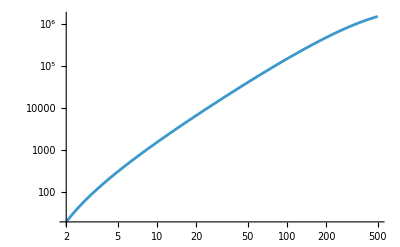

```mathematica
LogLogPlot[Rexact2//Abs,{r, 2.01, 500}, PlotRange->All]
```

```mathematica
α
```

-0.0000279945777111266781693427310952+4.02408033473563576867913516011×10^-29 ⅈ

```mathematica
HeunC[5.99 + 0.016 I,-0.0001119+4.59 10^-7 I, 1-0.068I,1+0.036121I, -0.000027+4.02 10^-29 I,   -0.05]//Quiet
```

1.31286+0.0228071 ⅈ

```mathematica
HeunC[5.99 + 0.016 I,-0.0001119+4.59 10^-7 I, 1-0.068I,1+0.036121I, -0.000027+4.02 10^-29 I,   -0.5]//Quiet
```

5.45862+0.389371 ⅈ

```mathematica
HeunC[5.99 + 0.016 I,-0.0001119+4.59 10^-7 I, 1-0.068I,1+0.036121I, -0.000027+4.02 10^-29 I,   -10^7]//Quiet
```

-3.57271×10^29+1.09064×10^29 ⅈ

```mathematica
DSolve[y''[x]==-αα y'[x],y[x],x]
```

{{y[x]→-(ⅇ^(-x αα) C[1])/αα+C[2]}}

```mathematica
Print[φ,φ+ν, 1+β,1+γ, α]
```

5.980973420695997864359850405186+0.16490404597960835914829372328673 ⅈ-0.0111883515501602840053276112421+0.000459463475094734358926773237759 ⅈ1.000000000000000003573632743639252070449-0.688962239286779325229560599218164 ⅈ0.999999999999999998127059276409674660877+0.361085071562813068192788919605586 ⅈ-0.00280265611835179059299595137855+1.93986564058566553838925643233×10^-17 ⅈ

```mathematica
1/0.002
```

500.

```mathematica
function2[r_]:=Interpolation[prova][r]
function2[10]
```

431541.

```mathematica
FindMaximum[Abs[Rexact2],{r, 20}]
```

SetPrecision::precsm: Requested precision 20.9818 is smaller than $MinPrecision. Using $MinPrecision instead.

N::precsm: Requested precision 20.9818 is smaller than $MinPrecision. Using $MinPrecision instead.

NumericalMath`FixedPrecisionEvaluate::precsm: Requested precision 20.9818 is smaller than $MinPrecision. Using $MinPrecision instead.

N::precsm: Requested precision 20.9818 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

NumericalMath`FixedPrecisionEvaluate::precsm: Requested precision 20.9818 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of NumericalMath`FixedPrecisionEvaluate::precsm will be suppressed during this calculation.

SetPrecision::precsm: Requested precision 20.9818 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of SetPrecision::precsm will be suppressed during this calculation.

SetPrecision::preclg: Requested precision 42.4377 is larger than $MaxPrecision. Using current $MaxPrecision of 40. instead. $MaxPrecision = Infinity specifies that any precision should be allowed.

N::preclg: Requested precision 42.4377 is larger than $MaxPrecision. Using current $MaxPrecision of 40. instead. $MaxPrecision = Infinity specifies that any precision should be allowed.

NumericalMath`FixedPrecisionEvaluate::preclg: Requested precision 42.4377 is larger than $MaxPrecision. Using current $MaxPrecision of 40. instead. $MaxPrecision = Infinity specifies that any precision should be allowed.

N::preclg: Requested precision 42.4377 is larger than $MaxPrecision. Using current $MaxPrecision of 40. instead. $MaxPrecision = Infinity specifies that any precision should be allowed.

General::stop: Further output of N::preclg will be suppressed during this calculation.

NumericalMath`FixedPrecisionEvaluate::preclg: Requested precision 42.4377 is larger than $MaxPrecision. Using current $MaxPrecision of 40. instead. $MaxPrecision = Infinity specifies that any precision should be allowed.

General::stop: Further output of NumericalMath`FixedPrecisionEvaluate::preclg will be suppressed during this calculation.

SetPrecision::preclg: Requested precision 54.2377 is larger than $MaxPrecision. Using current $MaxPrecision of 40. instead. $MaxPrecision = Infinity specifies that any precision should be allowed.

General::stop: Further output of SetPrecision::preclg will be suppressed during this calculation.

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{1.22662×10^244,{r→-7.06012×10^8}}

```mathematica
(*comparison of wavefuncitons-- we could normalize them properly by computing the mass of the cloud, here we do it quickly by aligning peaks*)
```

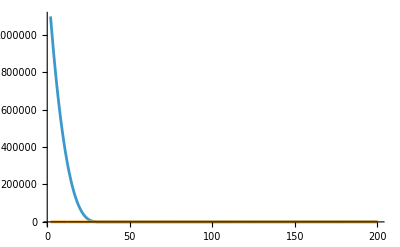

```mathematica
Plot[{function[r], Abs[Rexact2]/16.821816648057492*0.49},{r,2.01,200}, PlotRange->All]
```

They match! Let us compare the real parts of those wavefunctions with the hydrogenic approximation, which should fail to describe them properly as alpha=0.3 (we are relativistic). again we align them roughtly aligning peaks just for visual purposes

```mathematica
provare=Table[{rmap[ζ[j]],Re[(((r-rplus)/(r-rminus))^(I Pplus)(r-rminus)^(-1+(μ^2 M)/(√(μ^2-ω^2))-2M √(μ^2-ω^2))E^(-√(μ^2-ω^2)(r-rplus))BnumNorm[Iter][[j+1(Npoints+1)]](*[[j+1(Npoints+1)]]*))/.{ω->μ √(1-(μ^2 M^2)/(Nν[Iter])^2),r->rmap[ζ[j]]}]},{j,1,Npoints}]//Quiet;
```

```mathematica
functionre=Interpolation[provare]
```

InterpolatingFunction[…]

```mathematica
a0=1/μ^2;
```

```mathematica
RnHydro[nn_, l_, r_]:=√( ( 2/(nn a0))^3 Factorial[nn-l-1]/(2nn Factorial[nn+l]))((2 r)/(a0 nn))^l Exp[- r/(nn a0)]LaguerreL[nn-l-1,2 l+1,  (2 r)/(nn a0)]
```

```mathematica
FindMaximum[Re[Rexact2],{r, 20}]
FindMaximum[RnHydro[2,1,r],{r, 20}]
```

SetPrecision::precsm: Requested precision 22.0884 is smaller than $MinPrecision. Using $MinPrecision instead.

N::precsm: Requested precision 22.0884 is smaller than $MinPrecision. Using $MinPrecision instead.

NumericalMath`FixedPrecisionEvaluate::precsm: Requested precision 22.0884 is smaller than $MinPrecision. Using $MinPrecision instead.

N::precsm: Requested precision 22.0884 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

NumericalMath`FixedPrecisionEvaluate::precsm: Requested precision 22.0884 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of NumericalMath`FixedPrecisionEvaluate::precsm will be suppressed during this calculation.

SetPrecision::precsm: Requested precision 22.0884 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of SetPrecision::precsm will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{24550.7,{r→570691.}}

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{2.99132×10^-17,{r→20.}}

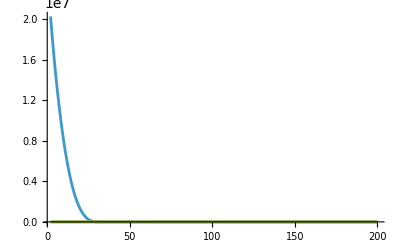

```mathematica
Plot[{Abs[functionre[r]], Re[Rexact2]/16.998734757125344*0.58,RnHydro[2,1,r]/0.0040550261297861495 *0.44},{r,2.01,200}, PlotRange->All]
```